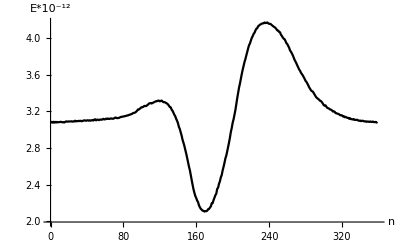

```mathematica
data = Import["/home/artem/projects/solver/build/trace/gloss_curve.txt", "Data"]//Flatten;
(*data = Import["/home/artem/projects/data_claster/trace/gloss_curve.txt", "Data"]//Flatten;*)
curve=Table[{i-2,data[[i]]/10^12}, {i,2,data[[1]]+1}];
pl=ListLinePlot[curve,PlotStyle->Directive[Black,PointSize[0.008]],
AxesLabel->{"n", "E*10^-12"},
AxesStyle->Directive[Black, 15],
PlotRange->All]
```